```mathematica
Clear["Global`*"]
```

```mathematica
μ=0.5;β=1./0.3;η=-0.07;nn=200;
k=Table[i/nn ⅇ^((7. i)/nn),{i,1,nn}];
τ1=Table[ⅇ^(-(Floor[nn/2]-i)/Floor[nn/2]5.) (β/2.-0.01),{i,1,Floor[nn/2]}];τ2=Table[β-τ1[[Floor[nn/2]+1-i]],{i,1,Floor[nn/2]}];
(*τ1=Table[β/2(1-ⅇ^(-(Floor[nn/2]-i)/Floor[nn/2]5.))+0.01 ,{i,Floor[nn/2],1,-1}];τ2=Table[β-τ1[[Floor[nn/2]+1-i]],{i,1,Floor[nn/2]}];*)
τ=Flatten[{τ1,τ2}];
(*τ=Table[ⅇ^(-(nn-i)/nn5.5)(β-0.02),{i,1,nn}];*)
ω=Flatten[{Table[ ((2 i-1) π)/β,{i,1,Floor[nn/2]}],((2 (Floor[nn/2]+2)-1) π)/β,Table[(2.(Floor[ⅇ^((i-Floor[nn/2])/Floor[nn/2] 6.+3)-ⅇ^3.]+i+1)-1)π/β,{i,Floor[nn/2]+2,nn}]}];
Ω=Flatten[{Table[ (2 (i) π)/β,{i,1,Floor[nn/2]}],((2 (Floor[nn/2]+2)) π)/β,Table[2.(Floor[ⅇ^((i-Floor[nn/2])/Floor[nn/2] 6.+3)-ⅇ^3.]+i+1)π/β,{i,Floor[nn/2]+2,nn-1}],0.}];
(*Ω=Table[2.(ⅇ^((i-1)/99. 9.)+i-2)π/β,{i,1,100}];*)
(*k=q[[1]];*)
dω=2π/β;
I0[ω_,τ_,j_]:=ⅇ^(-ⅈ ω[[j]] τ)(-dω/(2 ⅈ) Cot[(τ dω)/2.] (ⅇ^(-ⅈ τ (ω[[j+1]]-ω[[j]]))-1));
I1[ω_,τ_,j_]:=1/4 dω ⅇ^(-ⅈ τ ω[[j+1]]) Csc[(dω τ)/2]^2 (dω-dω ⅇ^(ⅈ τ (-ω[[j]]+ω[[j+1]]))-ⅈ (ω[[j]]-ω[[j+1]]) Sin[dω τ]);
I2[ω_,τ_,j_]:=1/4 dω ⅇ^(-ⅈ τ ω[[j+1]]) (2 ⅈ (ω[[j]]-ω[[j+1]])^2 Cot[(dω τ)/2]+dω (-2 ω[[j]]+2 ω[[j+1]]+ⅈ dω (-1+ⅇ^(ⅈ τ (ω[[j+1]]-ω[[j]]))) Cot[(dω τ)/2]) Csc[(dω τ)/2]^2);
I3[ω_,τ_,j_]:=1/8 dω ⅇ^(-ⅈ τ ω[[j+1]]) (-4 ⅈ (ω[[j]]-ω[[j+1]])^3 Cot[(dω τ)/2]+dω Csc[(dω τ)/2]^2 (-2 dω^2 (-1+ⅇ^(ⅈ τ (-ω[[j]]+ω[[j+1]])))+6 (ω[[j]]-ω[[j+1]])^2+3 dω Csc[(dω τ)/2]^2 (dω (-1+ⅇ^(ⅈ τ (ω[[j+1]]-ω[[j]])))+ⅈ (ω[[j]]-ω[[j+1]]) Sin[dω τ])));
J0[τ_]:=-dω/(2 ⅈ) Cot[(τ dω)/2.];
J1[τ_]:=1/4 dω^2 Csc[(dω τ)/2]^2;
J2[τ_]:=-1/4 ⅈ dω^3 Cot[(dω τ)/2] Csc[(dω τ)/2]^2;
J3[τ_]:=1/2 dω (-1/2 dω^3 Cot[(dω τ)/2]^2 Csc[(dω τ)/2]^2-1/4 dω^3 Csc[(dω τ)/2]^4);
```

```mathematica
ep[k_]:=k^2-4. μ
Γ[q_,Ω_]:=(16.π)/(2. η-√(ep[q]-2 ⅈ Ω));
x=Flatten[{Table[-Ω[[nn-i]],{i,1,nn-1}],Table[Ω[[i]],{i,1,nn-1}]}];
y=Flatten[{Table[Γ[k[[1]],-Ω[[nn-i]]],{i,1,nn-1}],Table[Γ[k[[1]],Ω[[i]]],{i,1,nn-1}]}];
n=Dimensions[x][[1]];
y1=Table[0,{i,1,n-1}];u=Table[0,{i,1,n-1}];

Do[sig=(x[[i]]-x[[i-1]])/(x[[i+1]]-x[[i-1]]);y1[[i]]=(sig-1.)/(sig*y1[[i-1]]+2.);u[[i]]=(6. (((y[[i+1]]-y[[i]])/(x[[i+1]]-x[[i]])-(y[[i]]-y[[i-1]])/(x[[i]]-x[[i-1]]))/(x[[i+1]]-x[[i-1]]))-sig*u[[i-1]])/(sig*y1[[i-1]]+2.),{i,2,n-1}]
y2=Flatten[{y1,0}];
Do[y2[[i]]=y2[[i]]*y2[[i+1]]+u[[i]],{i,n-1,1,-1}];

a=Table[y[[i]],{i,nn,2 nn-3}];
b=Table[(y[[i+1]]-y[[i]])/(x[[i+1]]-x[[i]])-((x[[i+1]]-x[[i]])*(2. y2[[i]]+y2[[i+1]]))/6.,{i,nn,2 nn-3}];
c=Table[y2[[i]]/2.,{i,nn,2 nn-3}];
d=Table[(y2[[i+1]]-y2[[i]])/(6.(x[[i+1]]-x[[i]])),{i,nn,2 nn-3}];
outmatrix=Table[(2.*Sum[Re[Γ[k[[1]],Ω[[i]]]*ⅇ^(-ⅈ Ω[[i]] τ[[j]])],{i,2,nn/2}])/β,{j,1,nn}];
f1=Re[Table[Table[I0[Ω,τ[[j]],i]*a[[i]]+I1[Ω,τ[[j]],i]*b[[i]]+I2[Ω,τ[[j]],i]*c[[i]]+I3[Ω,τ[[j]],i]*d[[i]],{i,nn/2+1,nn-2}]//Total,{j,1,nn}]]/π;
(*f2=2. Re[J0[τ]*(ⅇ^(-ⅈ Ω[[100]] τ)a[[99]]-ⅇ^(-ⅈ Ω[[2]]τ) a[[2]])+J1[τ]*(ⅇ^(-ⅈ Ω[[100]] τ)b[[99]]-ⅇ^(-ⅈ Ω[[2]]τ) b[[2]])+J2[τ]*(ⅇ^(-ⅈ Ω[[100]] τ)c[[99]]-ⅇ^(-ⅈ Ω[[2]]τ) c[[2]])+J3[τ]*(Table[(ⅇ^(-ⅈ Ω[[i+1]] τ)-ⅇ^(-ⅈ Ω[[i]] τ)) d[[i]],{i,2,99}]//Total)]+Re[I0[Ω,τ,1]*a[[1]]+I1[Ω,τ,1]*b[[1]]+I2[Ω,τ,1]*c[[1]]+I3[Ω,τ,1]*d[[1]]]*)
outmatrix=outmatrix+f1+Re[Γ[k[[1]],Ω[[nn]]]]/β
```

{-145.379,-159.311,-155.742,-138.764,-156.974,-133.864,-145.949,-134.741,-134.845,-132.709,-127.759,-126.667,-124.48,-117.193,-123.792,-107.499,-119.062,-107.381,-103.08,-111.197,-100.122,-94.0106,-100.606,-100.337,-91.7249,-85.762,-85.7677,-88.068,-89.4507,-89.2988,-88.2211,-86.7538,-84.9103,-82.1934,-78.0307,-73.042,-70.3115,-72.291,-72.8421,-65.1612,-63.3617,-65.5653,-57.8243,-62.671,-55.8451,-59.9972,-57.9628,-54.294,-56.2526,-56.8637,-54.6546,-51.7186,-49.3462,-47.7857,-46.0789,-42.9921,-42.3901,-45.7612,-41.485,-43.2753,-37.6153,-35.9099,-36.1064,-36.1304,-36.6334,-36.4473,-33.4684,-30.2075,-29.969,-26.7412,-28.8416,-30.4216,-28.5892,-25.5382,-23.4037,-22.7264,-25.5472,-21.5631,-18.7652,-19.0099,-20.1878,-18.8741,-16.4309,-16.3838,-17.1949,-14.2758,-13.269,-14.7454,-13.8186,-10.793,-13.4157,-10.0609,-9.12083,-11.3605,-7.47783,-7.88906,-7.60061,-5.74334,-6.61878,-3.87972,-6.5169,-1.97388,-5.12495,-1.48516,-2.84833,-1.44738,-0.24248,-1.7691,2.0281,0.127814,-0.141421,3.6632,2.66849,1.37161,3.01313,4.98135,5.42633,4.61125,3.92029,3.46215,4.04061,4.37802,4.48817,4.67251,4.80831,5.71261,7.1773,7.95228,6.8003,5.19995,6.83527,7.1835,4.8214,7.02686,4.28652,6.31911,3.88014,4.15995,4.87019,3.05761,1.72619,1.10242,0.485941,-0.214904,-1.17579,-1.80519,-1.75977,-2.45377,-4.38525,-3.97216,-4.51532,-5.54826,-6.466,-5.84946,-6.31847,-7.23263,-7.69686,-7.77433,-7.4756,-6.63974,-5.73292,-6.08443,-7.03491,-4.83688,-5.23576,-4.7336,-3.74577,-2.92782,-3.57861,-0.587285,-1.3903,-1.93182,0.00255719,2.24826,2.59547,2.56127,2.59087,3.30719,3.71562,4.73994,6.3015,7.69608,8.9229,8.38316,7.25284,7.4734,9.77475,12.1668,10.295,10.1819,13.8532,11.6133,11.8224,15.4823,12.3466,16.3671,13.6849,16.0659,15.6385,17.0326,16.046,18.4945,16.35,20.1165,16.7682,19.7806,18.639,18.0143,21.8931,18.8925,19.2129,22.3239,20.3239,19.65,22.6109,21.033,19.2763,23.4278,23.2262,22.1689,22.0325,24.5646,24.5514,22.7273,21.8408,24.0633,25.2669,25.1031,23.9221,23.7822,22.8629,25.811,25.8235,27.4504,25.3769,23.4825,23.8992,26.362,28.4732,26.6123,26.8268,26.575,24.5605,22.9579,26.5327,27.0368,26.466,26.511,26.7479,27.0998,28.1419,29.0011,26.0555,22.4395,27.2273,24.849,26.3545,26.9249,29.5428,25.6739,32.1331,30.0915,25.476,27.3848,30.946,31.7381,30.3108,28.5035,27.3757,27.2829,28.2756,30.0479,31.4685,30.4945,26.0892,21.9586,25.2059,33.5998,31.978,22.9901,30.1655,35.6215,23.1393,33.4233,31.6627,24.7481,37.5584,21.4047,38.5491,20.4651,38.7119,19.3127,38.6117,19.9045,34.1788,27.4971,22.0626,38.9295,16.2054,31.6016}

```mathematica
8*NIntegrate[(√z)/(4 η^2+z)*ⅇ^(-τ (ep[k[[1]]]+z)/2)/(ⅇ^(-β (ep[k[[1]]]+z)/2)-1),{z,0,∞},MaxRecursion->20, AccuracyGoal->8,Method->"PrincipalValue",Exclusions->-ep[k]]
```

{-164.092,-161.037,-158.033,-155.08,-152.176,-149.322,-146.515,-143.756,-141.043,-138.376,-135.755,-133.177,-130.644,-128.153,-125.704,-123.297,-120.93,-118.604,-116.317,-114.069,-111.86,-109.687,-107.552,-105.454,-103.391,-101.363,-99.3701,-97.4112,-95.4857,-93.5933,-91.7333,-89.9052,-88.1085,-86.3427,-84.6072,-82.9017,-81.2255,-79.5783,-77.9595,-76.3687,-74.8054,-73.2692,-71.7596,-70.2763,-68.8187,-67.3864,-65.9791,-64.5963,-63.2377,-61.9027,-60.5911,-59.3025,-58.0364,-56.7925,-55.5705,-54.3699,-53.1905,-52.0318,-50.8935,-49.7753,-48.6769,-47.5979,-46.5379,-45.4968,-44.4741,-43.4695,-42.4827,-41.5135,-40.5615,-39.6264,-38.7079,-37.8058,-36.9198,-36.0495,-35.1947,-34.3552,-33.5306,-32.7207,-31.9252,-31.1439,-30.3765,-29.6227,-28.8824,-28.1551,-27.4408,-26.7391,-26.0498,-25.3726,-24.7074,-24.0538,-23.4117,-22.7808,-22.1609,-21.5517,-20.953,-20.3647,-19.7863,-19.2178,-18.6589,-18.1094,-17.569,-17.0375,-16.5147,-16.0004,-15.4944,-14.9964,-14.5061,-14.0235,-13.5481,-13.0799,-12.6186,-12.1639,-11.7156,-11.2735,-10.8373,-10.4068,-9.98172,-9.56185,-9.14691,-8.73665,-8.33079,-7.92906,-7.53119,-7.13688,-6.74585,-6.35779,-5.97238,-5.58931,-5.20823,-4.82878,-4.45062,-4.07334,-3.69654,-3.31985,-2.94276,-2.56483,-2.18556,-1.80443,-1.42086,-1.03427,-0.644015,-0.249399,0.150316,0.555931,0.968315,1.38841,1.81724,2.25592,2.70569,3.16789,3.33761,3.79781,4.24274,4.6738,5.09215,5.49877,5.89449,6.28,6.65591,7.02272,7.38087,7.73074,8.07265,8.40691,8.73374,9.05338,9.36602,9.67184,9.97098,10.2636,10.5498,10.8298,11.1035,11.3713,11.633,11.8889,12.139,12.3835,12.6223,12.8556,13.0835,13.306,13.5233,13.7353,13.9423,14.1443,14.3412,14.5334,14.7207,14.9034,15.0814,15.2549,15.424,15.5887,15.7491,15.9052,16.0573,16.2053,16.3494,16.4896,16.6259,16.7586,16.8876,17.0131,17.1351,17.2537,17.369,17.481,17.5898,17.6956,17.7983,17.8981,17.9951,18.0892,18.1806,18.2693,18.3554,18.439,18.5201,18.5988,18.6752,18.7493,18.8212,18.891,18.9586,19.0242,19.0879,19.1496,19.2094,19.2674,19.3236,19.3781,19.431,19.4822,19.5318,19.5799,19.6265,19.6717,19.7155,19.7579,19.799,19.8388,19.8773,19.9147,19.9509,19.9859,20.0199,20.0527,20.0846,20.1154,20.1453,20.1742,20.2022,20.2293,20.2555,20.281,20.3056,20.3294,20.3525,20.3748,20.3964,20.4173,20.4376,20.4572,20.4762,20.4945,20.5123,20.5295,20.5462,20.5623,20.5779,20.593,20.6076,20.6218,20.6355,20.6487,20.6615,20.6739,20.6859,20.6975,20.7088,20.7196,20.7302,20.7404,20.7502,20.7597,20.769,20.7779,20.7865,20.7949,20.803,20.8108,20.8183,20.8257,20.8328,20.8396,20.8462,20.8526,20.8589,20.8649}

```mathematica
ep[k_]:=k^2-4. μ;
Γ[q_,Ω_]:=(16.π)/(2. η-√(ep[q]-2 ⅈ Ω));
x=Flatten[{Table[-Ω[[nn+1-i]],{i,1,nn-1}],Ω}];
n=Dimensions[x][[1]];
outmatrix={};f1={};

Do[y=Flatten[{Table[Γ[k[[i1]],-Ω[[nn+1-i]]],{i,1,nn-1}],Table[Γ[k[[i1]],Ω[[i]]],{i,1,nn}]}];
y1=Table[0,{i,1,n-1}];u=Table[0,{i,1,n-1}];
Do[sig=(x[[i]]-x[[i-1]])/(x[[i+1]]-x[[i-1]]);y1[[i]]=(sig-1.)/(sig*y1[[i-1]]+2.);u[[i]]=(6. (((y[[i+1]]-y[[i]])/(x[[i+1]]-x[[i]])-(y[[i]]-y[[i-1]])/(x[[i]]-x[[i-1]]))/(x[[i+1]]-x[[i-1]]))-sig*u[[i-1]])/(sig*y1[[i-1]]+2.),{i,2,n-1}]
y2=Flatten[{y1,0}];
Do[y2[[i]]=y2[[i]]*y2[[i+1]]+u[[i]],{i,n-1,1,-1}];

a=Table[y[[i]],{i,nn,2 nn-2}];
b=Table[(y[[i+1]]-y[[i]])/(x[[i+1]]-x[[i]])-((x[[i+1]]-x[[i]])*(2. y2[[i]]+y2[[i+1]]))/6.,{i,nn,2 nn-2}];
c=Table[y2[[i]]/2.,{i,nn,2 nn-2}];
d=Table[(y2[[i+1]]-y2[[i]])/(6.(x[[i+1]]-x[[i]])),{i,nn,2 nn-2}];

outmatrix0=(Re[Γ[k[[1]],Ω[[1]]]]+2.*Sum[Re[Γ[k[[i1]],Ω[[i]]]*ⅇ^(-ⅈ Ω[[i]] τ[[nn]])],{i,2,nn/2}])/β;
AppendTo[outmatrix,outmatrix0];
f0=Re[Table[I0[Ω,τ[[nn]],i]*a[[i]]+I1[Ω,τ[[nn]],i]*b[[i]]+I2[Ω,τ[[nn]],i]*c[[i]]+I3[Ω,τ[[nn]],i]*d[[i]],{i,nn/2+1,nn-1}]//Total]/π;
AppendTo[f1,f0];,{i1,1,nn}]
outmatrix=outmatrix+f1
```

{-5.05517,-5.05619,-5.05825,-5.06177,-5.06726,-5.07538,-5.08697,-5.1031,-5.12509,-5.15461,-5.19373,-5.24503,-5.31171,-5.39771,-5.5079,-5.64824,-5.82601,-6.04998,-6.33061,-6.67995,-7.11125,-7.63742,-8.26769,-9.00054,-9.8115,-10.6363,-11.359,-11.8252,-11.8912,-11.474,-10.5539,-9.13871,-7.23737,-4.86001,-2.03329,1.17555,4.62596,8.06082,11.0556,12.974,12.9648,10.0658,3.49078,-6.8828,-20.0116,-33.6287,-45.0432,-52.4923,-55.9267,-56.5183,-55.5525,-53.8063,-51.6185,-49.1671,-46.6011,-44.0384,-41.5495,-39.1658,-36.8978,-34.747,-32.713,-30.7949,-28.9925,-27.3059,-25.7346,-24.2771,-22.9304,-21.6902,-20.5508,-19.5054,-18.5457,-17.6619,-16.8428,-16.0754,-15.346,-14.641,-13.9486,-13.2605,-12.5731,-11.8873,-11.2075,-10.5403,-9.89229,-9.26953,-8.67642,-8.11582,-7.58918,-7.09678,-6.63805,-6.21186,-5.8167,-5.45087,-5.11256,-4.79995,-4.51125,-4.24474,-3.99878,-3.77183,-3.56244,-3.36927}

```mathematica
(*   FT from τ to ω   *)
```

```mathematica
I00[ω_,τ_,j_]:=ⅇ^(ⅈ τ[[j]] ω)((ⅇ^(ⅈ ω (τ[[j+1]]-τ[[j]]))-1)/(ⅈ ω));
I11[ω_,τ_,j_]:=(ⅇ^(ⅈ τ[[j]] ω) (-1+ⅇ^(ⅈ (-τ[[j]]+τ[[j+1]]) ω) (1+ⅈ (τ[[j]]-τ[[j+1]]) ω)))/ω^2;
I22[ω_,τ_,j_]:=1/ω^3 ⅇ^(ⅈ τ[[j+1]] ω) (2 ⅈ-2 ⅈ ⅇ^(ⅈ (τ[[j]]-τ[[j+1]]) ω)+(τ[[j]]-τ[[j+1]]) ω (-2-ⅈ (τ[[j]]-τ[[j+1]]) ω));
I33[ω_,τ_,j_]:=1/ω^4 ⅇ^(ⅈ τ[[j+1]] ω) (-6+6 ⅇ^(ⅈ (τ[[j]]-τ[[j+1]]) ω)+(τ[[j]]-τ[[j+1]]) ω (-6 ⅈ+(τ[[j]]-τ[[j+1]]) ω (3+ⅈ (τ[[j]]-τ[[j+1]]) ω)));
J00[ω_]:=-ⅈ/ω;
J11[ω_]:=1/ω^2 ;
J22[ω_]:=(2 ⅈ)/ω^3;
J33[ω_]:=-6/ω^4;

ep[k_]:=k^2- μ;
G[k_,τ_]:=ⅇ^(-ep[k] τ^2)(*ⅇ^(-ep[k] τ)/(ⅇ^(-β ep[k])+1.)*);
x=τ;
y=G[k[[65]],τ];
n=Dimensions[x][[1]];
y1=Table[0,{i,1,n-1}];u=Table[0,{i,1,n-1}];

Do[sig=(x[[i]]-x[[i-1]])/(x[[i+1]]-x[[i-1]]);y1[[i]]=(sig-1.)/(sig*y1[[i-1]]+2.);u[[i]]=(6. (((y[[i+1]]-y[[i]])/(x[[i+1]]-x[[i]])-(y[[i]]-y[[i-1]])/(x[[i]]-x[[i-1]]))/(x[[i+1]]-x[[i-1]]))-sig*u[[i-1]])/(sig*y1[[i-1]]+2.),{i,2,n-1}]
y2=Flatten[{y1,0}];
Do[y2[[i]]=y2[[i]]*y2[[i+1]]+u[[i]],{i,n-1,1,-1}];

a=Table[y[[i]],{i,1,nn-1}];
b=Table[(y[[i+1]]-y[[i]])/(x[[i+1]]-x[[i]])-((x[[i+1]]-x[[i]])*(2. y2[[i]]+y2[[i+1]]))/6.,{i,1,nn-1}];
c=Table[y2[[i]]/2.,{i,1,nn-1}];
d=Table[(y2[[i+1]]-y2[[i]])/(6.(x[[i+1]]-x[[i]])),{i,1,nn-1}];

f1=Table[Table[I00[ω[[j]],τ,i]*a[[i]]+I11[ω[[j]],τ,i]*b[[i]]+I22[ω[[j]],τ,i]*c[[i]]+I33[ω[[j]],τ,i]*d[[i]],{i,1,nn-1}]//Total,{j,1,nn}]
(*f2=J00[ω]*(ⅇ^(ⅈ ω τ[[nn-1]])a[[nn-1]]-ⅇ^(ⅈ ω τ[[1]]) a[[1]])+J11[ω]*(ⅇ^(ⅈ ω τ[[nn-1]])b[[nn-1]]-ⅇ^(ⅈ ω τ[[1]]) b[[1]])+J22[ω]*(ⅇ^(ⅈ ω τ[[nn-1]])c[[nn-1]]-ⅇ^(ⅈ ω τ[[1]]) c[[1]])+J33[ω]*(Table[(ⅇ^(ⅈ ω τ[[i+1]])-ⅇ^(ⅈ ω τ[[i]])) d[[i]],{i,1,nn-1}]//Total)*)
```

{0.806503+0.734228 ⅈ,0.0194563+0.423103 ⅈ,-0.0000474249+0.223572 ⅈ,-0.000271594+0.155759 ⅈ,-0.000382979+0.120045 ⅈ,-0.000445592+0.0977851 ⅈ,-0.00048362+0.0825351 ⅈ,-0.000508258+0.0714197 ⅈ,-0.000525062+0.0629524 ⅈ,-0.000537009+0.0562851 ⅈ,-0.000545793+0.0508977 ⅈ,-0.000552433+0.0464532 ⅈ,-0.000557572+0.0427236 ⅈ,-0.000561627+0.039549 ⅈ,-0.000564885+0.036814 ⅈ,-0.000567536+0.0344331 ⅈ,-0.000569727+0.0323416 ⅈ,-0.000571552+0.0304897 ⅈ,-0.000573094+0.0288384 ⅈ,-0.000574403+0.0273569 ⅈ,-0.000575528+0.0260201 ⅈ,-0.000576498+0.0248078 ⅈ,-0.000577343+0.0237035 ⅈ,-0.00057808+0.0226932 ⅈ,-0.00057873+0.0217655 ⅈ,-0.000579303+0.0209107 ⅈ,-0.000579812+0.0201204 ⅈ,-0.000580266+0.0193876 ⅈ,-0.000580672+0.0187062 ⅈ,-0.000581038+0.0180711 ⅈ,-0.000581366+0.0174776 ⅈ,-0.000581664+0.0169218 ⅈ,-0.000581932+0.0164003 ⅈ,-0.000582179+0.0159098 ⅈ,-0.000582398+0.0154478 ⅈ,-0.000582606+0.0150119 ⅈ,-0.000582787+0.0145997 ⅈ,-0.000582963+0.0142097 ⅈ,-0.000583114+0.0138398 ⅈ,-0.000583263+0.0134887 ⅈ,-0.000583391+0.0131548 ⅈ,-0.000583515+0.0128371 ⅈ,-0.000583629+0.0125343 ⅈ,-0.000583728+0.0122455 ⅈ,-0.000583832+0.0119695 ⅈ,-0.000583911+0.0117058 ⅈ,-0.000584002+0.0114533 ⅈ,-0.000584074+0.0112115 ⅈ,-0.000584143+0.0109796 ⅈ,-0.000584215+0.0107571 ⅈ,-0.000584268+0.0105434 ⅈ,-0.000584329+0.010338 ⅈ,-0.000584382+0.0101404 ⅈ,-0.000584425+0.00995016 ⅈ,-0.000584475+0.00976691 ⅈ,-0.000584515+0.00959024 ⅈ,-0.000584551+0.00941983 ⅈ,-0.000584589+0.00925533 ⅈ,-0.000584621+0.00909644 ⅈ,-0.000584649+0.00894289 ⅈ,-0.000584679+0.0087944 ⅈ,-0.000584705+0.00865073 ⅈ,-0.000584726+0.00851165 ⅈ,-0.000584748+0.00837694 ⅈ,-0.000584769+0.00824639 ⅈ,-0.000584785+0.00811982 ⅈ,-0.0005848+0.00799706 ⅈ,-0.000584815+0.00787791 ⅈ,-0.000584828+0.00776224 ⅈ,-0.000584838+0.00764989 ⅈ,-0.000584848+0.00754072 ⅈ,-0.000584857+0.00743459 ⅈ,-0.000584864+0.00733138 ⅈ,-0.000584869+0.00723097 ⅈ,-0.000584874+0.00713325 ⅈ,-0.000584878+0.00703811 ⅈ,-0.00058488+0.00694545 ⅈ,-0.000584881+0.00685517 ⅈ,-0.000584882+0.00676718 ⅈ,-0.000584881+0.0066814 ⅈ,-0.00058488+0.00659774 ⅈ,-0.000584877+0.00651613 ⅈ,-0.000584874+0.00643648 ⅈ,-0.00058487+0.00635874 ⅈ,-0.000584865+0.00628283 ⅈ,-0.000584859+0.00620869 ⅈ,-0.000584853+0.00613625 ⅈ,-0.000584846+0.00606547 ⅈ,-0.000584838+0.00599627 ⅈ,-0.000584829+0.00592862 ⅈ,-0.00058482+0.00586245 ⅈ,-0.000584811+0.00579772 ⅈ,-0.0005848+0.00573439 ⅈ,-0.000584789+0.0056724 ⅈ,-0.000584777+0.00561172 ⅈ,-0.000584765+0.0055523 ⅈ,-0.000584752+0.00549411 ⅈ,-0.000584738+0.0054371 ⅈ,-0.000584725+0.00538125 ⅈ,-0.00058471+0.00532651 ⅈ,-0.000584695+0.00527285 ⅈ,-0.00058468+0.00522024 ⅈ,-0.000584664+0.00516866 ⅈ,-0.000584647+0.00511806 ⅈ,-0.00058463+0.00506843 ⅈ,-0.000584613+0.00501973 ⅈ,-0.000584595+0.00497195 ⅈ,-0.000584577+0.00492504 ⅈ,-0.000584558+0.00487899 ⅈ,-0.000584539+0.00483378 ⅈ,-0.000584519+0.00478938 ⅈ,-0.000584499+0.00474577 ⅈ,-0.000584478+0.00470293 ⅈ,-0.000584458+0.00466084 ⅈ,-0.000584436+0.00461948 ⅈ,-0.000584414+0.00457883 ⅈ,-0.000584392+0.00453887 ⅈ,-0.00058437+0.00449959 ⅈ,-0.000584347+0.00446096 ⅈ,-0.000584324+0.00442297 ⅈ,-0.0005843+0.00438561 ⅈ,-0.000584276+0.00434886 ⅈ,-0.000584252+0.00431271 ⅈ,-0.000584227+0.00427713 ⅈ,-0.000584202+0.00424212 ⅈ,-0.000584177+0.00420767 ⅈ,-0.000584151+0.00417375 ⅈ,-0.000584124+0.00414036 ⅈ,-0.000584098+0.00410749 ⅈ,-0.000584071+0.00407511 ⅈ,-0.000584044+0.00404323 ⅈ,-0.000584017+0.00401183 ⅈ,-0.000583989+0.0039809 ⅈ,-0.000583961+0.00395043 ⅈ,-0.000583932+0.0039204 ⅈ,-0.000583903+0.00389081 ⅈ,-0.000583874+0.00386166 ⅈ,-0.000583845+0.00383292 ⅈ,-0.000583815+0.00380459 ⅈ,-0.000583785+0.00377666 ⅈ,-0.000583755+0.00374913 ⅈ,-0.000583724+0.00372198 ⅈ,-0.000583693+0.00369521 ⅈ,-0.000583662+0.0036688 ⅈ,-0.00058363+0.00364276 ⅈ,-0.000583598+0.00361707 ⅈ,-0.000583566+0.00359172 ⅈ,-0.000583534+0.00356672 ⅈ,-0.000583501+0.00354205 ⅈ,-0.000583468+0.0035177 ⅈ,-0.000583401+0.00346996 ⅈ,-0.000583332+0.00342345 ⅈ,-0.000583298+0.00340064 ⅈ,-0.000583263+0.00337811 ⅈ,-0.000583228+0.00335588 ⅈ,-0.000583192+0.00333392 ⅈ,-0.000583157+0.00331223 ⅈ,-0.000583121+0.00329081 ⅈ,-0.000583085+0.00326965 ⅈ,-0.000583048+0.00324875 ⅈ,-0.000583011+0.00322811 ⅈ,-0.000582974+0.00320771 ⅈ,-0.000582899+0.00316765 ⅈ,-0.000582861+0.00314797 ⅈ,-0.000582823+0.00312852 ⅈ,-0.000582785+0.0031093 ⅈ,-0.000582746+0.00309031 ⅈ,-0.000582707+0.00307153 ⅈ,-0.000582668+0.00305297 ⅈ,-0.000582628+0.00303461 ⅈ,-0.000582548+0.00299853 ⅈ,-0.000582508+0.00298079 ⅈ,-0.000582467+0.00296325 ⅈ,-0.000582426+0.00294591 ⅈ,-0.000582385+0.00292875 ⅈ,-0.000582302+0.002895 ⅈ,-0.00058226+0.0028784 ⅈ,-0.000582218+0.00286197 ⅈ,-0.000582175+0.00284572 ⅈ,-0.000582133+0.00282965 ⅈ,-0.000582046+0.002798 ⅈ,-0.000582003+0.00278243 ⅈ,-0.000581959+0.00276702 ⅈ,-0.000581871+0.00273667 ⅈ,-0.000581826+0.00272172 ⅈ,-0.000581781+0.00270693 ⅈ,-0.000581691+0.0026778 ⅈ,-0.000581645+0.00266345 ⅈ,-0.000581553+0.00263518 ⅈ,-0.000581507+0.00262125 ⅈ,-0.00058146+0.00260746 ⅈ,-0.000581366+0.00258028 ⅈ,-0.000581319+0.00256689 ⅈ,-0.000581223+0.00254048 ⅈ,-0.000581127+0.00251458 ⅈ,-0.000581078+0.00250181 ⅈ,-0.00058098+0.00247663 ⅈ,-0.000580931+0.00246421 ⅈ,-0.000580831+0.00243972 ⅈ,-0.000580731+0.00241568 ⅈ,-0.000580629+0.00239206 ⅈ,-0.000580527+0.00236887 ⅈ,-0.000580475+0.00235743 ⅈ,-0.000580371+0.00233484 ⅈ,-0.000580266+0.00231265 ⅈ,-0.00058016+0.00229084 ⅈ,-0.000580053+0.00226941 ⅈ,-0.00057989+0.00223793 ⅈ,-0.000579781+0.00221738 ⅈ,-0.00057967+0.00219718 ⅈ,-0.000579559+0.0021773 ⅈ,-0.00057939+0.00214809 ⅈ,-0.000579276+0.002129 ⅈ,-0.000579103+0.00210094 ⅈ,-0.000578929+0.00207354 ⅈ,-0.000578811+0.00205562 ⅈ,-0.000578632+0.00202926 ⅈ,-0.000578452+0.00200349 ⅈ,-0.000578269+0.00197831 ⅈ,-0.000578084+0.00195367 ⅈ,-0.000577834+0.00192167 ⅈ,-0.000577643+0.00189826 ⅈ,-0.000577387+0.00186782 ⅈ,-0.000577191+0.00184555 ⅈ,-0.000576928+0.00181656 ⅈ,-0.000576661+0.00178836 ⅈ,-0.000576389+0.00176091 ⅈ,-0.000576045+0.0017276 ⅈ,-0.000575765+0.00170173 ⅈ,-0.00057541+0.0016703 ⅈ,-0.00057505+0.00163985 ⅈ,-0.000574683+0.00161033 ⅈ,-0.00057431+0.00158169 ⅈ,-0.000573855+0.00154843 ⅈ,-0.000573392+0.00151632 ⅈ,-0.00057292+0.0014853 ⅈ,-0.00057244+0.0014553 ⅈ,-0.000571869+0.00142154 ⅈ,-0.000571286+0.00138902 ⅈ,-0.000570693+0.00135768 ⅈ,-0.000570001+0.00132322 ⅈ,-0.000569293+0.00129012 ⅈ,-0.000568572+0.00125829 ⅈ,-0.000567742+0.00122391 ⅈ,-0.000566894+0.00119094 ⅈ,-0.00056593+0.00115586 ⅈ,-0.000564943+0.00112229 ⅈ,-0.000563832+0.001087 ⅈ,-0.000562693+0.00105329 ⅈ,-0.00056142+0.00101819 ⅈ,-0.000560115+0.000984714 ⅈ,-0.000558664+0.000950131 ⅈ,-0.000557061+0.000914697 ⅈ,-0.000555414+0.000880991 ⅈ,-0.000553602+0.000846641 ⅈ,-0.000551615+0.000811848 ⅈ,-0.000549573+0.000778802 ⅈ,-0.00054721+0.000743537 ⅈ,-0.000544778+0.000710123 ⅈ,-0.000541996+0.000674974 ⅈ,-0.000539131+0.000641721 ⅈ,-0.000536033+0.000608664 ⅈ,-0.000532537+0.000574442 ⅈ,-0.000528775+0.000540739 ⅈ,-0.000524899+0.000508894 ⅈ,-0.000520403+0.00047508 ⅈ,-0.000515767+0.000443196 ⅈ,-0.000510633+0.000410894 ⅈ,-0.000504973+0.000378379 ⅈ,-0.000498947+0.000346788 ⅈ,-0.000492346+0.000315207 ⅈ,-0.00048514+0.000283784 ⅈ,-0.000477298+0.000252649 ⅈ,-0.000469008+0.00022266 ⅈ,-0.000459817+0.000192383 ⅈ,-0.000449906+0.000162703 ⅈ,-0.000439017+0.000133095 ⅈ,-0.000427349+0.000104326 ⅈ,-0.000414886+0.0000764611 ⅈ,-0.00040136+0.0000490753 ⅈ,-0.000386485+0.0000218911 ⅈ,-0.000370755-3.98981×10^-6 ⅈ,-0.000353908-0.000028896 ⅈ,-0.000335672-0.0000530157 ⅈ,-0.00031605-0.0000760949 ⅈ,-0.000295344-0.0000976118 ⅈ,-0.000273039-0.000117906 ⅈ,-0.000249768-0.000136227 ⅈ,-0.00022506-0.000152794 ⅈ,-0.000199047-0.000167289 ⅈ,-0.000171904-0.00017941 ⅈ,-0.00014385-0.000188876 ⅈ,-0.000114893-0.000195478 ⅈ,-0.0000856375-0.000198891 ⅈ,-0.0000559782-0.000198917 ⅈ,-0.0000266573-0.000195317 ⅈ,1.99652×10^-6-0.000187913 ⅈ,0.0000293374-0.000176618 ⅈ,0.0000548308-0.000161363 ⅈ,0.000077542-0.000142422 ⅈ}

```mathematica
NIntegrate[ G[k[[65]],τ0] ⅇ^(ⅈ τ0 ω),{τ0,0,β}]
```

{0.80709+0.734228 ⅈ,0.0200426+0.423104 ⅈ,0.000538926+0.223573 ⅈ,0.000314775+0.15576 ⅈ,0.000203379+0.120047 ⅈ,0.000140769+0.0977869 ⅈ,0.000102738+0.0825372 ⅈ,0.0000780989+0.0714221 ⅈ,0.0000612924+0.0629552 ⅈ,0.0000493438+0.0562882 ⅈ,0.0000405576+0.0509011 ⅈ,0.0000339143+0.046457 ⅈ,0.0000287727+0.0427277 ⅈ,0.0000247136+0.0395535 ⅈ,0.0000214541+0.0368188 ⅈ,0.0000187977+0.0344382 ⅈ,0.0000166047+0.032347 ⅈ,0.0000147734+0.0304954 ⅈ,0.0000132286+0.0288445 ⅈ,0.0000119136+0.0273633 ⅈ,0.0000107851+0.0260268 ⅈ,9.8095×10^-6+0.0248149 ⅈ,8.96032×10^-6+0.0237109 ⅈ,8.2167×10^-6+0.022701 ⅈ,7.56185×10^-6+0.0217736 ⅈ,6.9822×10^-6+0.0209191 ⅈ,6.46667×10^-6+0.0201291 ⅈ,6.00615×10^-6+0.0193966 ⅈ,5.59309×10^-6+0.0187156 ⅈ,5.22119×10^-6+0.0180808 ⅈ,4.88516×10^-6+0.0174877 ⅈ,4.58054×10^-6+0.0169322 ⅈ,4.30353×10^-6+0.016411 ⅈ,4.05089×10^-6+0.0159209 ⅈ,3.81985×10^-6+0.0154592 ⅈ,3.60802×10^-6+0.0150235 ⅈ,3.41332×10^-6+0.0146118 ⅈ,3.23396×10^-6+0.014222 ⅈ,3.06837×10^-6+0.0138524 ⅈ,2.91518×10^-6+0.0135016 ⅈ,2.77317×10^-6+0.0131682 ⅈ,2.64129×10^-6+0.0128508 ⅈ,2.51859×10^-6+0.0125483 ⅈ,2.40425×10^-6+0.0122598 ⅈ,2.29752×10^-6+0.0119842 ⅈ,2.19773×10^-6+0.0117207 ⅈ,2.10431×10^-6+0.0114686 ⅈ,2.01672×10^-6+0.0112271 ⅈ,1.93448×10^-6+0.0109956 ⅈ,1.85718×10^-6+0.0107734 ⅈ,1.78441×10^-6+0.01056 ⅈ,1.71584×10^-6+0.0103549 ⅈ,1.65114×10^-6+0.0101577 ⅈ,1.59004×10^-6+0.00996776 ⅈ,1.53226×10^-6+0.00978484 ⅈ,1.47758×10^-6+0.0096085 ⅈ,1.42577×10^-6+0.00943842 ⅈ,1.37664×10^-6+0.00927424 ⅈ,1.33001×10^-6+0.00911569 ⅈ,1.2857×10^-6+0.00896246 ⅈ,1.24357×10^-6+0.0088143 ⅈ,1.20348×10^-6+0.00867096 ⅈ,1.1653×10^-6+0.0085322 ⅈ,1.1289×10^-6+0.00839782 ⅈ,1.09419×10^-6+0.00826761 ⅈ,1.06105×10^-6+0.00814137 ⅈ,1.02939×10^-6+0.00801893 ⅈ,9.99129×10^-7+0.00790012 ⅈ,9.70182×10^-7+0.00778477 ⅈ,9.42476×10^-7+0.00767275 ⅈ,9.15939×10^-7+0.00756391 ⅈ,8.90508×10^-7+0.00745811 ⅈ,8.66121×10^-7+0.00735523 ⅈ,8.42722×10^-7+0.00725515 ⅈ,8.20259×10^-7+0.00715775 ⅈ,7.98682×10^-7+0.00706294 ⅈ,7.77945×10^-7+0.0069706 ⅈ,7.58005×10^-7+0.00688065 ⅈ,7.38822×10^-7+0.00679299 ⅈ,7.20358×10^-7+0.00670754 ⅈ,7.02578×10^-7+0.00662421 ⅈ,6.85447×10^-7+0.00654293 ⅈ,6.68936×10^-7+0.00646361 ⅈ,6.53014×10^-7+0.0063862 ⅈ,6.37654×10^-7+0.00631062 ⅈ,6.2283×10^-7+0.0062368 ⅈ,6.08516×10^-7+0.0061647 ⅈ,5.9469×10^-7+0.00609424 ⅈ,5.8133×10^-7+0.00602537 ⅈ,5.68415×10^-7+0.00595805 ⅈ,5.55926×10^-7+0.00589221 ⅈ,5.43844×10^-7+0.00582781 ⅈ,5.32152×10^-7+0.0057648 ⅈ,5.20832×10^-7+0.00570314 ⅈ,5.0987×10^-7+0.00564279 ⅈ,4.9925×10^-7+0.0055837 ⅈ,4.88959×10^-7+0.00552583 ⅈ,4.78983×10^-7+0.00546915 ⅈ,4.69309×10^-7+0.00541363 ⅈ,4.59925×10^-7+0.00535921 ⅈ,4.50819×10^-7+0.00530589 ⅈ,4.41982×10^-7+0.00525361 ⅈ,4.33401×10^-7+0.00520235 ⅈ,4.25068×10^-7+0.00515208 ⅈ,4.16974×10^-7+0.00510278 ⅈ,4.09108×10^-7+0.00505441 ⅈ,4.01462×10^-7+0.00500695 ⅈ,3.94029×10^-7+0.00496037 ⅈ,3.86801×10^-7+0.00491465 ⅈ,3.79769×10^-7+0.00486977 ⅈ,3.72928×10^-7+0.00482569 ⅈ,3.6627×10^-7+0.00478241 ⅈ,3.59788×10^-7+0.0047399 ⅈ,3.53477×10^-7+0.00469814 ⅈ,3.47331×10^-7+0.0046571 ⅈ,3.41344×10^-7+0.00461678 ⅈ,3.3551×10^-7+0.00457715 ⅈ,3.29824×10^-7+0.0045382 ⅈ,3.24282×10^-7+0.0044999 ⅈ,3.18878×10^-7+0.00446224 ⅈ,3.13608×10^-7+0.00442521 ⅈ,3.08468×10^-7+0.00438878 ⅈ,3.03453×10^-7+0.00435296 ⅈ,2.98559×10^-7+0.00431771 ⅈ,2.93783×10^-7+0.00428303 ⅈ,2.8912×10^-7+0.0042489 ⅈ,2.84568×10^-7+0.00421531 ⅈ,2.80122×10^-7+0.00418225 ⅈ,2.7578×10^-7+0.0041497 ⅈ,2.71537×10^-7+0.00411765 ⅈ,2.67392×10^-7+0.0040861 ⅈ,2.63341×10^-7+0.00405503 ⅈ,2.59382×10^-7+0.00402442 ⅈ,2.55511×10^-7+0.00399428 ⅈ,2.51726×10^-7+0.00396458 ⅈ,2.48025×10^-7+0.00393532 ⅈ,2.44404×10^-7+0.00390649 ⅈ,2.40863×10^-7+0.00387808 ⅈ,2.37397×10^-7+0.00385007 ⅈ,2.34006×10^-7+0.00382247 ⅈ,2.30688×10^-7+0.00379527 ⅈ,2.27439×10^-7+0.00376844 ⅈ,2.24258×10^-7+0.003742 ⅈ,2.21144×10^-7+0.00371592 ⅈ,2.18094×10^-7+0.00369021 ⅈ,2.15107×10^-7+0.00366484 ⅈ,2.1218×10^-7+0.00363983 ⅈ,2.09313×10^-7+0.00361515 ⅈ,2.06504×10^-7+0.0035908 ⅈ,2.03751×10^-7+0.00356678 ⅈ,1.98407×10^-7+0.0035197 ⅈ,1.93271×10^-7+0.00347384 ⅈ,1.90778×10^-7+0.00345135 ⅈ,1.88332×10^-7+0.00342916 ⅈ,1.85933×10^-7+0.00340724 ⅈ,1.8358×10^-7+0.00338561 ⅈ,1.81271×10^-7+0.00336425 ⅈ,1.79005×10^-7+0.00334316 ⅈ,1.76782×10^-7+0.00332233 ⅈ,1.74599×10^-7+0.00330175 ⅈ,1.72457×10^-7+0.00328144 ⅈ,1.70354×10^-7+0.00326137 ⅈ,1.66262×10^-7+0.00322195 ⅈ,1.64271×10^-7+0.0032026 ⅈ,1.62316×10^-7+0.00318348 ⅈ,1.60395×10^-7+0.00316459 ⅈ,1.58508×10^-7+0.00314592 ⅈ,1.56654×10^-7+0.00312747 ⅈ,1.54833×10^-7+0.00310923 ⅈ,1.53043×10^-7+0.0030912 ⅈ,1.49555×10^-7+0.00305577 ⅈ,1.47856×10^-7+0.00303836 ⅈ,1.46185×10^-7+0.00302115 ⅈ,1.44543×10^-7+0.00300413 ⅈ,1.42928×10^-7+0.0029873 ⅈ,1.39778×10^-7+0.0029542 ⅈ,1.38242×10^-7+0.00293792 ⅈ,1.36732×10^-7+0.00292182 ⅈ,1.35246×10^-7+0.0029059 ⅈ,1.33784×10^-7+0.00289015 ⅈ,1.3093×10^-7+0.00285915 ⅈ,1.29537×10^-7+0.0028439 ⅈ,1.28166×10^-7+0.00282882 ⅈ,1.25489×10^-7+0.00279912 ⅈ,1.24182×10^-7+0.0027845 ⅈ,1.22896×10^-7+0.00277004 ⅈ,1.20381×10^-7+0.00274155 ⅈ,1.19153×10^-7+0.00272753 ⅈ,1.16752×10^-7+0.00269991 ⅈ,1.15579×10^-7+0.00268631 ⅈ,1.14423×10^-7+0.00267284 ⅈ,1.12163×10^-7+0.00264631 ⅈ,1.11058×10^-7+0.00263324 ⅈ,1.08896×10^-7+0.00260749 ⅈ,1.06797×10^-7+0.00258223 ⅈ,1.05771×10^-7+0.00256979 ⅈ,1.03761×10^-7+0.00254526 ⅈ,1.02777×10^-7+0.00253317 ⅈ,1.00852×10^-7+0.00250932 ⅈ,9.89801×10^-8+0.00248593 ⅈ,9.71599×10^-8+0.00246296 ⅈ,9.53894×10^-8+0.00244042 ⅈ,9.45223×10^-8+0.0024293 ⅈ,9.28231×10^-8+0.00240736 ⅈ,9.11693×10^-8+0.00238582 ⅈ,8.95594×10^-8+0.00236466 ⅈ,8.79917×10^-8+0.00234387 ⅈ,8.57162×10^-8+0.00231337 ⅈ,8.42479×10^-8+0.00229347 ⅈ,8.2817×10^-8+0.0022739 ⅈ,8.14223×10^-8+0.00225467 ⅈ,7.93953×10^-8+0.00222643 ⅈ,7.80858×10^-8+0.00220799 ⅈ,7.61814×10^-8+0.0021809 ⅈ,7.43458×10^-8+0.00215447 ⅈ,7.31587×10^-8+0.0021372 ⅈ,7.14307×10^-8+0.0021118 ⅈ,6.97632×10^-8+0.00208701 ⅈ,6.81533×10^-8+0.00206279 ⅈ,6.65986×10^-8+0.00203912 ⅈ,6.4607×10^-8+0.0020084 ⅈ,6.31714×10^-8+0.00198596 ⅈ,6.13305×10^-8+0.00195681 ⅈ,6.00021×10^-8+0.0019355 ⅈ,5.8297×10^-8+0.0019078 ⅈ,5.66636×10^-8+0.00188088 ⅈ,5.50979×10^-8+0.00185471 ⅈ,5.32304×10^-8+0.00182301 ⅈ,5.18038×10^-8+0.00179841 ⅈ,5.00999×10^-8+0.00176859 ⅈ,4.84787×10^-8+0.00173974 ⅈ,4.69349×10^-8+0.00171181 ⅈ,4.54637×10^-8+0.00168477 ⅈ,4.37878×10^-8+0.00165342 ⅈ,4.22029×10^-8+0.00162323 ⅈ,4.07025×10^-8+0.00159411 ⅈ,3.92807×10^-8+0.00156602 ⅈ,3.77142×10^-8+0.00153447 ⅈ,3.62395×10^-8+0.00150417 ⅈ,3.48496×10^-8+0.00147505 ⅈ,3.33569×10^-8+0.00144311 ⅈ,3.19581×10^-8+0.00141253 ⅈ,3.06455×10^-8+0.00138321 ⅈ,2.92632×10^-8+0.00135166 ⅈ,2.79723×10^-8+0.00132151 ⅈ,2.66358×10^-8+0.00128955 ⅈ,2.53927×10^-8+0.0012591 ⅈ,2.41233×10^-8+0.00122722 ⅈ,2.29468×10^-8+0.00119692 ⅈ,2.17588×10^-8+0.00116553 ⅈ,2.06608×10^-8+0.00113574 ⅈ,1.95624×10^-8+0.00110514 ⅈ,1.84748×10^-8+0.00107398 ⅈ,1.74754×10^-8+0.00104452 ⅈ,1.6492×10^-8+0.00101471 ⅈ,1.55318×10^-8+0.000984725 ⅈ,1.46531×10^-8+0.000956464 ⅈ,1.37508×10^-8+0.000926548 ⅈ,1.29294×10^-8+0.000898447 ⅈ,1.21001×10^-8+0.000869158 ⅈ,1.13482×10^-8+0.000841718 ⅈ,1.06316×10^-8+0.000814711 ⅈ,9.92204×10^-9+0.000787053 ⅈ,9.25474×10^-9+0.000760126 ⅈ,8.65257×10^-9+0.000734981 ⅈ,8.04279×10^-9+0.000708609 ⅈ,7.49528×10^-9+0.000684065 ⅈ,6.96723×10^-9+0.000659528 ⅈ,6.46218×10^-9+0.000635174 ⅈ,5.99633×10^-9+0.000611851 ⅈ,5.55448×10^-9+0.000588877 ⅈ,5.13783×10^-9+0.00056636 ⅈ,4.74692×10^-9+0.000544388 ⅈ,4.39034×10^-9+0.000523543 ⅈ,4.04948×10^-9+0.000502808 ⅈ,3.73327×10^-9+0.000482778 ⅈ,3.43473×10^-9+0.000463073 ⅈ,3.16007×10^-9+0.000444172 ⅈ,2.90776×10^-9+0.000426071 ⅈ,2.67219×10^-9+0.000408448 ⅈ,2.44969×10^-9+0.000391073 ⅈ,2.24753×10^-9+0.00037459 ⅈ,2.06106×10^-9+0.000358714 ⅈ,1.88712×10^-9+0.000343243 ⅈ,1.72576×10^-9+0.000328241 ⅈ,1.57866×10^-9+0.000313941 ⅈ,1.44146×10^-9+0.000299988 ⅈ,1.31713×10^-9+0.000286759 ⅈ,1.20202×10^-9+0.000273942 ⅈ,1.09597×10^-9+0.000261579 ⅈ,9.9867×10^-10+0.000249697 ⅈ,9.09694×10^-10+0.000238314 ⅈ,8.27847×10^-10+0.000227341 ⅈ,7.53496×10^-10+0.000216892 ⅈ,6.84994×10^-10+0.000206798 ⅈ,6.22655×10^-10+0.000197163 ⅈ,5.65652×10^-10+0.000187922 ⅈ,5.1371×10^-10+0.000179086 ⅈ,4.66211×10^-10+0.000170606 ⅈ,4.23196×10^-10+0.000162545 ⅈ}

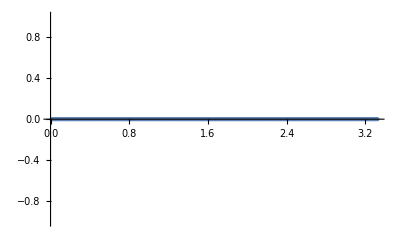

```mathematica
ListPlot[Table[{x[[i]],Im[y2[[i]]]},{i,1,n}]]
```

```mathematica
s1={};ynn={};
(*Do[klo=1;khi=n;s=x[[1]]+(x[[n]]-x[[1]])/n*(j-1);s1=AppendTo[s1,s];
While[khi-klo>1,i=Floor[(khi+klo)/2];If[x[[i]]>s,khi=i,klo=i]];
yn=a[[i]]+b[[i]]*(s-x[[i]])+c[[i]]*(s-x[[i]])^2+d[[i]] (s-x[[i]])^3;ynn=AppendTo[ynn,yn],{j,1,300}]*)
Do[klo=1;khi=nn-1;s=Ω[[1]]+(Ω[[nn-1]]-Ω[[1]])/(nn-1)*(j-1);s1=AppendTo[s1,s];
While[khi-klo>1,i=Floor[(khi+klo)/2];If[Ω[[i]]>s,khi=i,klo=i]];
yn=a[[i]]+b[[i]]*(s-Ω[[i]])+c[[i]]*(s-Ω[[i]])^2+d[[i]] (s-Ω[[i]])^3;ynn=AppendTo[ynn,yn],{j,1,298}]
```

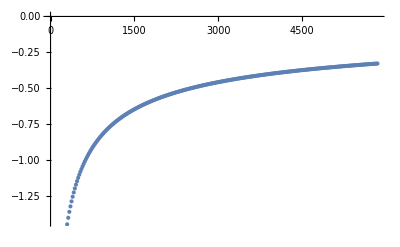

```mathematica
ListPlot[Table[{s1[[i]],Re[ynn[[i]]]},{i,1,298}]]
```

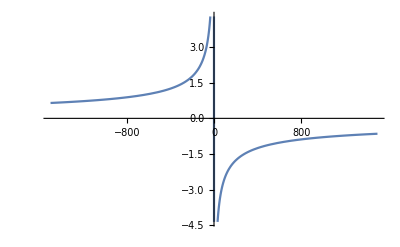

```mathematica
f=Interpolation[Table[{x[[i]],Im[y[[i]]]},{i,1,n}], Method->"Spline"];
Plot[f[kk],{kk,-5000,1500}]
```

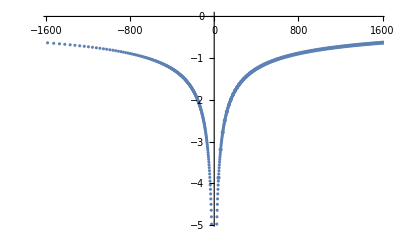

```mathematica
Show[%206,%342]
```

```mathematica
ep[k_]:=k^2- μ;
G[k_,τ_]:=ⅇ^(-ep[k] τ)/(ⅇ^(-β ep[k])+1.);
Manipulate[Plot[Re[G[k[[65]],ττ] ⅇ^(ⅈ ττ ω[[i]])],{ττ,0,β}],{i,1,10,1}]
```

Plot::plln: Limiting value β in {ττ,0,β} is not a machine-sized real number.

```mathematica
I00[ω_,τ_,j_]:=ⅇ^(ⅈ τ[[j]] ω)((ⅇ^(ⅈ ω (τ[[j+1]]-τ[[j]]))-1)/(ⅈ ω));
I11[ω_,τ_,j_]:=(ⅇ^(ⅈ τ[[j]] ω) (-1+ⅇ^(ⅈ (-τ[[j]]+τ[[j+1]]) ω) (1+ⅈ (τ[[j]]-τ[[j+1]]) ω)))/ω^2;
I22[ω_,τ_,j_]:=1/ω^3 ⅇ^(ⅈ τ[[j+1]] ω) (2 ⅈ-2 ⅈ ⅇ^(ⅈ (τ[[j]]-τ[[j+1]]) ω)+(τ[[j]]-τ[[j+1]]) ω (-2-ⅈ (τ[[j]]-τ[[j+1]]) ω));
I33[ω_,τ_,j_]:=1/ω^4 ⅇ^(ⅈ τ[[j+1]] ω) (-6+6 ⅇ^(ⅈ (τ[[j]]-τ[[j+1]]) ω)+(τ[[j]]-τ[[j+1]]) ω (-6 ⅈ+(τ[[j]]-τ[[j+1]]) ω (3+ⅈ (τ[[j]]-τ[[j+1]]) ω)));
J00[ω_]:=-ⅈ/ω;
J11[ω_]:=1/ω^2 ;
J22[ω_]:=(2 ⅈ)/ω^3;
J33[ω_]:=-6/ω^4;

ep[k_]:=k^2-4. μ;

x=τ;
y=8*NIntegrate[(√z)/(4 η^2+z)*ⅇ^(-τ (ep[k[[1]]]+z)/2)/(ⅇ^(-β (ep[k[[1]]]+z)/2)-1),{z,0,∞},MaxRecursion->20, AccuracyGoal->8,Method->"PrincipalValue",Exclusions->-ep[k]];
n=Dimensions[x][[1]];
y1=Table[0,{i,1,n-1}];u=Table[0,{i,1,n-1}];
Do[sig=(x[[i]]-x[[i-1]])/(x[[i+1]]-x[[i-1]]);y1[[i]]=(sig-1.)/(sig*y1[[i-1]]+2.);u[[i]]=(6. (((y[[i+1]]-y[[i]])/(x[[i+1]]-x[[i]])-(y[[i]]-y[[i-1]])/(x[[i]]-x[[i-1]]))/(x[[i+1]]-x[[i-1]]))-sig*u[[i-1]])/(sig*y1[[i-1]]+2.),{i,2,n-1}]
y2=Flatten[{y1,0}];
Do[y2[[i]]=y2[[i]]*y2[[i+1]]+u[[i]],{i,n-1,1,-1}];

a=Table[y[[i]],{i,1,nn-1}];
b=Table[(y[[i+1]]-y[[i]])/(x[[i+1]]-x[[i]])-((x[[i+1]]-x[[i]])*(2. y2[[i]]+y2[[i+1]]))/6.,{i,1,nn-1}];
c=Table[y2[[i]]/2.,{i,1,nn-1}];
d=Table[(y2[[i+1]]-y2[[i]])/(6.(x[[i+1]]-x[[i]])),{i,1,nn-1}];

f1=Table[Table[I00[Ω[[j]],τ,i]*a[[i]]+I11[Ω[[j]],τ,i]*b[[i]]+I22[Ω[[j]],τ,i]*c[[i]]+I33[Ω[[j]],τ,i]*d[[i]],{i,1,nn-1}]//Total,{j,1,nn-1}]
```

{-9.40853-19.375 ⅈ,-7.36723-13.3489 ⅈ,-5.81929-10.681 ⅈ,-4.74417-9.12054 ⅈ,-3.95608-8.0667 ⅈ,-3.35003-7.29149 ⅈ,-2.86658-6.68818 ⅈ,-2.46995-6.19954 ⅈ,-2.13737-5.79184 ⅈ,-1.8536-5.44377 ⅈ,-1.60802-5.14113 ⅈ,-1.39301-4.87405 ⅈ,-1.20291-4.63543 ⅈ,-1.03345-4.42 ⅈ,-0.881326-4.22379 ⅈ,-0.743928-4.04371 ⅈ,-0.619181-3.87733 ⅈ,-0.505405-3.72272 ⅈ,-0.401221-3.5783 ⅈ,-0.305484-3.44279 ⅈ,-0.21724-3.31512 ⅈ,-0.135685-3.1944 ⅈ,-0.0601325-3.07987 ⅈ,0.0100062-2.97091 ⅈ,0.0752358-2.86696 ⅈ,0.135995-2.76755 ⅈ,0.192669-2.67227 ⅈ,0.245595-2.58077 ⅈ,0.295068-2.49274 ⅈ,0.34135-2.40789 ⅈ,0.384677-2.326 ⅈ,0.425257-2.24685 ⅈ,0.463274-2.17024 ⅈ,0.498901-2.09601 ⅈ,0.532288-2.024 ⅈ,0.563573-1.95408 ⅈ,0.592879-1.88612 ⅈ,0.620323-1.82001 ⅈ,0.646008-1.75565 ⅈ,0.670028-1.69295 ⅈ,0.692473-1.63183 ⅈ,0.713424-1.57221 ⅈ,0.732953-1.51401 ⅈ,0.751129-1.45718 ⅈ,0.768018-1.40166 ⅈ,0.783678-1.3474 ⅈ,0.798165-1.29434 ⅈ,0.81153-1.24244 ⅈ,0.823824-1.19166 ⅈ,0.835088-1.14196 ⅈ,0.845366-1.0933 ⅈ,0.854698-1.04566 ⅈ,0.863123-0.998992 ⅈ,0.870674-0.953278 ⅈ,0.877386-0.908489 ⅈ,0.883291-0.8646 ⅈ,0.888418-0.821587 ⅈ,0.892795-0.77943 ⅈ,0.89645-0.738109 ⅈ,0.89941-0.697605 ⅈ,0.901697-0.657899 ⅈ,0.903337-0.618977 ⅈ,0.904351-0.58082 ⅈ,0.904761-0.543416 ⅈ,0.904587-0.50675 ⅈ,0.903849-0.470811 ⅈ,0.902567-0.435584 ⅈ,0.900758-0.40106 ⅈ,0.898441-0.367226 ⅈ,0.895632-0.334073 ⅈ,0.892347-0.30159 ⅈ,0.888603-0.269769 ⅈ,0.884415-0.238601 ⅈ,0.879798-0.208077 ⅈ,0.874766-0.17819 ⅈ,0.869333-0.14893 ⅈ,0.863512-0.120292 ⅈ,0.857318-0.0922672 ⅈ,0.850762-0.0648504 ⅈ,0.843857-0.0380346 ⅈ,0.836616-0.0118134 ⅈ,0.82905+0.0138194 ⅈ,0.821171+0.0388697 ⅈ,0.81299+0.0633429 ⅈ,0.804517+0.0872443 ⅈ,0.795765+0.110579 ⅈ,0.786743+0.133353 ⅈ,0.777462+0.15557 ⅈ,0.767931+0.177237 ⅈ,0.758162+0.198357 ⅈ,0.748162+0.218935 ⅈ,0.737943+0.238976 ⅈ,0.727512+0.258484 ⅈ,0.71688+0.277464 ⅈ,0.706055+0.29592 ⅈ,0.695047+0.313857 ⅈ,0.683863+0.331279 ⅈ,0.672512+0.34819 ⅈ,0.661003+0.364594 ⅈ,0.649343+0.380496 ⅈ,0.637542+0.395899 ⅈ,0.625607+0.410808 ⅈ,0.613545+0.425227 ⅈ,0.601364+0.43916 ⅈ,0.589072+0.452611 ⅈ,0.576677+0.465584 ⅈ,0.564185+0.478083 ⅈ,0.551604+0.490113 ⅈ,0.538941+0.501677 ⅈ,0.526203+0.51278 ⅈ,0.513397+0.523426 ⅈ,0.500529+0.533619 ⅈ,0.487606+0.543363 ⅈ,0.474635+0.552661 ⅈ,0.461623+0.56152 ⅈ,0.448575+0.569942 ⅈ,0.435498+0.577931 ⅈ,0.422397+0.585494 ⅈ,0.40928+0.592632 ⅈ,0.396152+0.599351 ⅈ,0.383019+0.605656 ⅈ,0.369887+0.61155 ⅈ,0.356761+0.617038 ⅈ,0.343646+0.622124 ⅈ,0.33055+0.626814 ⅈ,0.317476+0.63111 ⅈ,0.304431+0.635019 ⅈ,0.291419+0.638544 ⅈ,0.278445+0.641691 ⅈ,0.265515+0.644463 ⅈ,0.252634+0.646866 ⅈ,0.239807+0.648904 ⅈ,0.227037+0.650583 ⅈ,0.214331+0.651906 ⅈ,0.201692+0.652878 ⅈ,0.189125+0.653505 ⅈ,0.176635+0.653792 ⅈ,0.164225+0.653742 ⅈ,0.151901+0.653362 ⅈ,0.139666+0.652656 ⅈ,0.127524+0.65163 ⅈ,0.11548+0.650287 ⅈ,0.103537+0.648634 ⅈ,0.0916998+0.646676 ⅈ,0.0799711+0.644417 ⅈ,0.0683548+0.641863 ⅈ,0.0568547+0.639019 ⅈ,0.0454741+0.63589 ⅈ,0.0342166+0.632481 ⅈ,0.0230853+0.628798 ⅈ,0.00121443+0.62063 ⅈ,-0.0201138+0.611429 ⅈ,-0.030567+0.606454 ⅈ,-0.0408759+0.601237 ⅈ,-0.0510378+0.595783 ⅈ,-0.06105+0.590098 ⅈ,-0.07091+0.584186 ⅈ,-0.0806154+0.578054 ⅈ,-0.0901638+0.571707 ⅈ,-0.0995529+0.56515 ⅈ,-0.108781+0.558388 ⅈ,-0.117845+0.551428 ⅈ,-0.135474+0.536934 ⅈ,-0.144035+0.52941 ⅈ,-0.152426+0.52171 ⅈ,-0.160643+0.513839 ⅈ,-0.168686+0.505802 ⅈ,-0.176553+0.497604 ⅈ,-0.184242+0.489252 ⅈ,-0.191753+0.480751 ⅈ,-0.206232+0.463322 ⅈ,-0.213199+0.454405 ⅈ,-0.219983+0.445361 ⅈ,-0.226582+0.436195 ⅈ,-0.232996+0.426912 ⅈ,-0.245265+0.408019 ⅈ,-0.251118+0.398419 ⅈ,-0.256784+0.388725 ⅈ,-0.262262+0.37894 ⅈ,-0.26755+0.369071 ⅈ,-0.27756+0.349102 ⅈ,-0.282281+0.339012 ⅈ,-0.286812+0.328858 ⅈ,-0.295305+0.308382 ⅈ,-0.299268+0.29807 ⅈ,-0.303041+0.287715 ⅈ,-0.310021+0.266897 ⅈ,-0.313229+0.256444 ⅈ,-0.319082+0.235475 ⅈ,-0.321728+0.224968 ⅈ,-0.324188+0.214454 ⅈ,-0.328555+0.19342 ⅈ,-0.330463+0.18291 ⅈ,-0.333734+0.161927 ⅈ,-0.336283+0.141023 ⅈ,-0.33729+0.130612 ⅈ,-0.338777+0.109895 ⅈ,-0.339258+0.0995975 ⅈ,-0.339706+0.0791446 ⅈ,-0.339477+0.0589094 ⅈ,-0.338583+0.0389242 ⅈ,-0.337039+0.0192203 ⅈ,-0.336028+0.00948324 ⅈ,-0.333537-0.00974246 ⅈ,-0.330435-0.0286132 ⅈ,-0.326738-0.0471015 ⅈ,-0.322463-0.0651808 ⅈ,-0.315007-0.0914775 ⅈ,-0.309369-0.108426 ⅈ,-0.303218-0.124881 ⅈ,-0.296576-0.140822 ⅈ,-0.285736-0.163725 ⅈ,-0.277956-0.178295 ⅈ,-0.265508-0.199058 ⅈ,-0.252194-0.218466 ⅈ,-0.242875-0.230629 ⅈ,-0.228286-0.247678 ⅈ,-0.213037-0.263262 ⅈ,-0.197204-0.277353 ⅈ,-0.180868-0.289927 ⅈ,-0.158437-0.304306 ⅈ,-0.141231-0.313287 ⅈ,-0.117926-0.322856 ⅈ,-0.100276-0.328232 ⅈ,-0.0766567-0.333024 ⅈ,-0.0531017-0.335139 ⅈ,-0.0297816-0.334636 ⅈ,-0.0012119-0.330446 ⅈ,0.0209891-0.324358 ⅈ,0.0476809-0.313508 ⅈ,0.0729473-0.299285 ⅈ,0.0965454-0.281961 ⅈ,0.118258-0.261832 ⅈ,0.14156-0.234423 ⅈ,0.161603-0.204015 ⅈ,0.178175-0.171213 ⅈ,0.191127-0.136643 ⅈ,0.20155-0.0949129 ⅈ,0.2069-0.0526236 ⅈ,0.207254-0.0107402 ⅈ,0.201785+0.0354521 ⅈ,0.190466+0.0786443 ⅈ,0.173876+0.117704 ⅈ,0.149792+0.155505 ⅈ,0.121081+0.185754 ⅈ,0.0853003+0.209565 ⅈ,0.0472067+0.222503 ⅈ,0.00483606+0.224097 ⅈ,-0.0357346+0.213024 ⅈ,-0.0754213+0.187957 ⅈ,-0.108055+0.151631 ⅈ,-0.133396+0.102999 ⅈ,-0.147521+0.0445988 ⅈ,-0.147531-0.0146451 ⅈ,-0.132771-0.0730381 ⅈ,-0.102846-0.123338 ⅈ,-0.0625387-0.156299 ⅈ,-0.0113529-0.169224 ⅈ,0.0384265-0.156374 ⅈ,0.083387-0.116132 ⅈ,0.110371-0.0573481 ⅈ,0.115327+0.0115029 ⅈ,0.0940967+0.0789199 ⅈ,0.0496625+0.124359 ⅈ,-0.00470869+0.134629 ⅈ,-0.0596035+0.104081 ⅈ,-0.0913335+0.0418411 ⅈ,-0.0899451-0.0348558 ⅈ,-0.0517869-0.0960141 ⅈ,0.00749314-0.111841 ⅈ,0.061609-0.072624 ⅈ,0.0804521+0.00495919 ⅈ,0.049998+0.0767642 ⅈ,-0.0109296+0.0950375 ⅈ,-0.0624607+0.044487 ⅈ,-0.0618496-0.0390261 ⅈ,-0.00642438-0.0847325 ⅈ,0.0521063-0.0458208 ⅈ,0.0529441+0.0385158 ⅈ,-0.00660352+0.0745447 ⅈ,-0.0546125+0.0135362 ⅈ,-0.0236181-0.0618778 ⅈ,0.0403914-0.0401149 ⅈ,0.0340421+0.0454591 ⅈ,-0.032686+0.0429624 ⅈ,-0.0306766-0.0421396 ⅈ,0.0350636-0.0313363 ⅈ,0.0156784+0.0487639 ⅈ,-0.0389105+0.00343216 ⅈ,0.013112-0.0449746 ⅈ,0.0221139+0.0360536 ⅈ,-0.0339332+0.000850617 ⅈ,0.0222342-0.0303184 ⅈ,-0.00228642+0.0397781 ⅈ,-0.0129839-0.0341883 ⅈ,0.0212203+0.0238258 ⅈ,-0.0239095-0.0156198 ⅈ,0.0237767+0.012011 ⅈ,-0.0218911-0.0136956 ⅈ}

```mathematica
(16.π)/(2. η-√(ep[k[[1]]]-2 ⅈ Ω))
```

{-13.2073-19.4059 ⅈ,-11.1655-13.4109 ⅈ,-9.61676-10.774 ⅈ,-8.54048-9.24443 ⅈ,-7.75092-8.22151 ⅈ,-7.14307-7.4772 ⅈ,-6.65749-6.90475 ⅈ,-6.25841-6.44692 ⅈ,-5.92305-6.06998 ⅈ,-5.63617-5.75262 ⅈ,-5.38716-5.48062 ⅈ,-5.1684-5.24412 ⅈ,-4.97423-5.036 ⅈ,-4.80037-4.85099 ⅈ,-4.64353-4.68511 ⅈ,-4.5011-4.53526 ⅈ,-4.371-4.39902 ⅈ,-4.25155-4.27445 ⅈ,-4.14139-4.15995 ⅈ,-4.03936-4.05425 ⅈ,-3.94451-3.95626 ⅈ,-3.85603-3.86509 ⅈ,-3.77326-3.77999 ⅈ,-3.69559-3.70031 ⅈ,-3.62253-3.62549 ⅈ,-3.55363-3.55506 ⅈ,-3.48852-3.4886 ⅈ,-3.42686-3.42576 ⅈ,-3.36836-3.36621 ⅈ,-3.31275-3.30969 ⅈ,-3.25981-3.25593 ⅈ,-3.20933-3.20472 ⅈ,-3.16112-3.15588 ⅈ,-3.11502-3.10921 ⅈ,-3.07088-3.06456 ⅈ,-3.02857-3.02179 ⅈ,-2.98795-2.98077 ⅈ,-2.94893-2.94139 ⅈ,-2.9114-2.90354 ⅈ,-2.87526-2.86712 ⅈ,-2.84044-2.83204 ⅈ,-2.80685-2.79822 ⅈ,-2.77443-2.7656 ⅈ,-2.74311-2.73409 ⅈ,-2.71282-2.70365 ⅈ,-2.68351-2.6742 ⅈ,-2.65514-2.6457 ⅈ,-2.62764-2.61809 ⅈ,-2.60098-2.59134 ⅈ,-2.57512-2.56539 ⅈ,-2.55001-2.54022 ⅈ,-2.52563-2.51577 ⅈ,-2.50193-2.49201 ⅈ,-2.47888-2.46892 ⅈ,-2.45646-2.44647 ⅈ,-2.43464-2.42462 ⅈ,-2.41339-2.40334 ⅈ,-2.39268-2.38262 ⅈ,-2.3725-2.36243 ⅈ,-2.35283-2.34274 ⅈ,-2.33363-2.32354 ⅈ,-2.31489-2.30481 ⅈ,-2.2966-2.28653 ⅈ,-2.27874-2.26867 ⅈ,-2.26129-2.25123 ⅈ,-2.24423-2.23419 ⅈ,-2.22755-2.21753 ⅈ,-2.21124-2.20123 ⅈ,-2.19528-2.1853 ⅈ,-2.17967-2.1697 ⅈ,-2.16438-2.15444 ⅈ,-2.14941-2.1395 ⅈ,-2.13474-2.12486 ⅈ,-2.12037-2.11052 ⅈ,-2.10629-2.09647 ⅈ,-2.09248-2.08269 ⅈ,-2.07895-2.06919 ⅈ,-2.06567-2.05595 ⅈ,-2.05264-2.04295 ⅈ,-2.03986-2.0302 ⅈ,-2.02731-2.01769 ⅈ,-2.01499-2.00541 ⅈ,-2.00289-1.99335 ⅈ,-1.99101-1.98151 ⅈ,-1.97934-1.96987 ⅈ,-1.96787-1.95844 ⅈ,-1.95659-1.94721 ⅈ,-1.94551-1.93617 ⅈ,-1.93462-1.92531 ⅈ,-1.9239-1.91464 ⅈ,-1.91336-1.90414 ⅈ,-1.903-1.89381 ⅈ,-1.8928-1.88365 ⅈ,-1.88276-1.87365 ⅈ,-1.87288-1.86381 ⅈ,-1.86315-1.85413 ⅈ,-1.85358-1.84459 ⅈ,-1.84415-1.8352 ⅈ,-1.83486-1.82596 ⅈ,-1.82571-1.81685 ⅈ,-1.8167-1.80787 ⅈ,-1.80782-1.79903 ⅈ,-1.79907-1.79032 ⅈ,-1.79044-1.78174 ⅈ,-1.78194-1.77327 ⅈ,-1.77355-1.76493 ⅈ,-1.76529-1.7567 ⅈ,-1.75714-1.74859 ⅈ,-1.7491-1.74059 ⅈ,-1.74117-1.7327 ⅈ,-1.73334-1.72491 ⅈ,-1.72563-1.71723 ⅈ,-1.71801-1.70966 ⅈ,-1.71049-1.70218 ⅈ,-1.70307-1.6948 ⅈ,-1.69575-1.68751 ⅈ,-1.68852-1.68032 ⅈ,-1.68138-1.67322 ⅈ,-1.67434-1.66621 ⅈ,-1.66738-1.65928 ⅈ,-1.6605-1.65245 ⅈ,-1.65371-1.64569 ⅈ,-1.64701-1.63902 ⅈ,-1.64038-1.63243 ⅈ,-1.63383-1.62592 ⅈ,-1.62736-1.61949 ⅈ,-1.62097-1.61313 ⅈ,-1.61465-1.60685 ⅈ,-1.60841-1.60064 ⅈ,-1.60224-1.5945 ⅈ,-1.59613-1.58843 ⅈ,-1.5901-1.58243 ⅈ,-1.58414-1.5765 ⅈ,-1.57824-1.57063 ⅈ,-1.5724-1.56483 ⅈ,-1.56663-1.5591 ⅈ,-1.56093-1.55343 ⅈ,-1.55528-1.54781 ⅈ,-1.5497-1.54226 ⅈ,-1.54418-1.53677 ⅈ,-1.53871-1.53134 ⅈ,-1.53331-1.52596 ⅈ,-1.52796-1.52064 ⅈ,-1.52266-1.51538 ⅈ,-1.51742-1.51017 ⅈ,-1.51223-1.50501 ⅈ,-1.5071-1.49991 ⅈ,-1.50202-1.49486 ⅈ,-1.49699-1.48986 ⅈ,-1.49201-1.48491 ⅈ,-1.48219-1.47515 ⅈ,-1.47257-1.46559 ⅈ,-1.46783-1.46088 ⅈ,-1.46313-1.45621 ⅈ,-1.45848-1.45158 ⅈ,-1.45387-1.44701 ⅈ,-1.44931-1.44247 ⅈ,-1.44479-1.43798 ⅈ,-1.44031-1.43352 ⅈ,-1.43587-1.42911 ⅈ,-1.43148-1.42474 ⅈ,-1.42712-1.42041 ⅈ,-1.41852-1.41187 ⅈ,-1.41428-1.40766 ⅈ,-1.41008-1.40348 ⅈ,-1.40592-1.39934 ⅈ,-1.40179-1.39524 ⅈ,-1.3977-1.39117 ⅈ,-1.39364-1.38714 ⅈ,-1.38962-1.38315 ⅈ,-1.38168-1.37526 ⅈ,-1.37776-1.37136 ⅈ,-1.37387-1.3675 ⅈ,-1.37002-1.36367 ⅈ,-1.3662-1.35988 ⅈ,-1.35865-1.35238 ⅈ,-1.35493-1.34867 ⅈ,-1.35123-1.345 ⅈ,-1.34756-1.34136 ⅈ,-1.34393-1.33774 ⅈ,-1.33674-1.3306 ⅈ,-1.33319-1.32708 ⅈ,-1.32967-1.32358 ⅈ,-1.32271-1.31666 ⅈ,-1.31927-1.31324 ⅈ,-1.31586-1.30985 ⅈ,-1.30911-1.30315 ⅈ,-1.30578-1.29984 ⅈ,-1.29918-1.29328 ⅈ,-1.29592-1.29005 ⅈ,-1.29269-1.28683 ⅈ,-1.28629-1.28047 ⅈ,-1.28313-1.27733 ⅈ,-1.27687-1.27111 ⅈ,-1.2707-1.26498 ⅈ,-1.26765-1.26195 ⅈ,-1.26161-1.25596 ⅈ,-1.25863-1.25299 ⅈ,-1.25272-1.24712 ⅈ,-1.2469-1.24133 ⅈ,-1.24115-1.23562 ⅈ,-1.23548-1.22999 ⅈ,-1.23268-1.22721 ⅈ,-1.22713-1.22169 ⅈ,-1.22165-1.21625 ⅈ,-1.21625-1.21088 ⅈ,-1.21091-1.20558 ⅈ,-1.20304-1.19776 ⅈ,-1.19788-1.19263 ⅈ,-1.19278-1.18757 ⅈ,-1.18775-1.18257 ⅈ,-1.18032-1.17519 ⅈ,-1.17544-1.17034 ⅈ,-1.16824-1.16319 ⅈ,-1.16117-1.15616 ⅈ,-1.15652-1.15155 ⅈ,-1.14966-1.14473 ⅈ,-1.14292-1.13803 ⅈ,-1.13629-1.13145 ⅈ,-1.12978-1.12498 ⅈ,-1.12127-1.11652 ⅈ,-1.11502-1.11031 ⅈ,-1.10683-1.10218 ⅈ,-1.10081-1.0962 ⅈ,-1.09294-1.08837 ⅈ,-1.08523-1.08071 ⅈ,-1.07768-1.07321 ⅈ,-1.06846-1.06405 ⅈ,-1.06125-1.05689 ⅈ,-1.05245-1.04814 ⅈ,-1.04386-1.03961 ⅈ,-1.03547-1.03128 ⅈ,-1.02729-1.02315 ⅈ,-1.01772-1.01364 ⅈ,-1.00841-1.00439 ⅈ,-0.999355-0.995388 ⅈ,-0.990537-0.986627 ⅈ,-0.98054-0.976693 ⅈ,-0.970839-0.967053 ⅈ,-0.961421-0.957694 ⅈ,-0.950985-0.947324 ⅈ,-0.940883-0.937285 ⅈ,-0.931095-0.927558 ⅈ,-0.920441-0.91697 ⅈ,-0.910145-0.906737 ⅈ,-0.8991-0.895761 ⅈ,-0.888447-0.885173 ⅈ,-0.877156-0.873951 ⅈ,-0.866285-0.863146 ⅈ,-0.854874-0.851804 ⅈ,-0.843903-0.840899 ⅈ,-0.832481-0.829545 ⅈ,-0.820685-0.817819 ⅈ,-0.809377-0.806577 ⅈ,-0.797765-0.795033 ⅈ,-0.785913-0.783251 ⅈ,-0.774575-0.771977 ⅈ,-0.762387-0.75986 ⅈ,-0.750758-0.748296 ⅈ,-0.73844-0.736048 ⅈ,-0.726709-0.724383 ⅈ,-0.714975-0.712713 ⅈ,-0.702753-0.700558 ⅈ,-0.690645-0.688516 ⅈ,-0.679142-0.677075 ⅈ,-0.666863-0.664862 ⅈ,-0.655228-0.653288 ⅈ,-0.643385-0.641506 ⅈ,-0.631409-0.629592 ⅈ,-0.619722-0.617965 ⅈ,-0.60799-0.606291 ⅈ,-0.596266-0.594626 ⅈ,-0.584598-0.583015 ⅈ,-0.573307-0.571779 ⅈ,-0.561851-0.560378 ⅈ,-0.550557-0.549137 ⅈ,-0.539215-0.537847 ⅈ,-0.528105-0.526788 ⅈ,-0.517242-0.515974 ⅈ,-0.50644-0.50522 ⅈ,-0.49556-0.494388 ⅈ,-0.485012-0.483885 ⅈ,-0.47463-0.473547 ⅈ,-0.464289-0.463249 ⅈ,-0.454036-0.453038 ⅈ,-0.444042-0.443084 ⅈ,-0.434068-0.43315 ⅈ,-0.424395-0.423514 ⅈ,-0.414807-0.413963 ⅈ,-0.405344-0.404535 ⅈ,-0.396035-0.395261 ⅈ,-0.386907-0.386167 ⅈ,-0.377899-0.37719 ⅈ,-0.369116-0.368438 ⅈ,-0.360428-0.359779 ⅈ,-0.351935-0.351315 ⅈ,-0.343591-0.342999 ⅈ,-0.335419-0.334853 ⅈ,-0.327384-0.326843 ⅈ,-3.48446+35.1982 ⅈ}

```mathematica
f[τ_?NumericQ]:=8*NIntegrate[(√z)/(4 η^2+z)*ⅇ^(-τ (ep[k[[1]]]+z)/2)/(ⅇ^(-β (ep[k[[1]]]+z)/2)-1),{z,0,∞},Method->"PrincipalValue",Exclusions->-ep[k]]
NIntegrate[f[ττ]*ⅇ^(ⅈ ττ Ω),{ττ,0,β},MaxRecursion->20, AccuracyGoal->8]
```

$Aborted

```mathematica
ListPlot[Table[{x[[i]],y[[i]]},{i,1,n}]]
```

```mathematica
ep[k_]:=k^2- μ;
G[k_,τ_]:=ⅇ^(-ep[k] τ^2);
Manipulate[Plot[Im[G[k[[65]],ττ] ⅇ^(ⅈ ττ ω[[i]])],{ττ,0,β}],{i,1,30,1}]
```

Plot::plln: Limiting value β in {ττ,0,β} is not a machine-sized real number.

```mathematica
μ=0.5;β=1./0.3;η=-0.07;nn=100;
k=Table[i/nn ⅇ^((7. i)/nn),{i,1,nn}];
τ1=Table[ⅇ^(-(Floor[nn/2]-i)/Floor[nn/2]5.) (β/2.-0.01),{i,1,Floor[nn/2]}];τ2=Table[β-τ1[[Floor[nn/2]+1-i]],{i,1,Floor[nn/2]}];
τ=Flatten[{τ1,τ2}];
ω=Flatten[{Table[ ((2 i-1) π)/β,{i,1,Floor[nn/2]}],((2 (Floor[nn/2]+2)-1) π)/β,Table[(2.(Floor[ⅇ^((i-Floor[nn/2])/Floor[nn/2] 5.+2.)-ⅇ^2.]+i+1)-1)π/β,{i,Floor[nn/2]+2,nn}]}];
Ω=Flatten[{Table[ (2 (i) π)/β,{i,1,Floor[nn/2]}],((2 (Floor[nn/2]+2)) π)/β,Table[2.(Floor[ⅇ^((i-Floor[nn/2])/Floor[nn/2] 5.+2.)-ⅇ^2.]+i+1)π/β,{i,Floor[nn/2]+2,nn-1}],0.}];
dω=2π/β;
I0[ω_,τ_,j_]:=ⅇ^(-ⅈ ω[[j]] τ)(-dω/(2 ⅈ) Cot[(τ dω)/2.] (ⅇ^(-ⅈ τ (ω[[j+1]]-ω[[j]]))-1));
I1[ω_,τ_,j_]:=1/4 dω ⅇ^(-ⅈ τ ω[[j+1]]) Csc[(dω τ)/2]^2 (dω-dω ⅇ^(ⅈ τ (-ω[[j]]+ω[[j+1]]))-ⅈ (ω[[j]]-ω[[j+1]]) Sin[dω τ]);
I2[ω_,τ_,j_]:=1/4 dω ⅇ^(-ⅈ τ ω[[j+1]]) (2 ⅈ (ω[[j]]-ω[[j+1]])^2 Cot[(dω τ)/2]+dω (-2 ω[[j]]+2 ω[[j+1]]+ⅈ dω (-1+ⅇ^(ⅈ τ (ω[[j+1]]-ω[[j]]))) Cot[(dω τ)/2]) Csc[(dω τ)/2]^2);
I3[ω_,τ_,j_]:=1/8 dω ⅇ^(-ⅈ τ ω[[j+1]]) (-4 ⅈ (ω[[j]]-ω[[j+1]])^3 Cot[(dω τ)/2]+dω Csc[(dω τ)/2]^2 (-2 dω^2 (-1+ⅇ^(ⅈ τ (-ω[[j]]+ω[[j+1]])))+6 (ω[[j]]-ω[[j+1]])^2+3 dω Csc[(dω τ)/2]^2 (dω (-1+ⅇ^(ⅈ τ (ω[[j+1]]-ω[[j]])))+ⅈ (ω[[j]]-ω[[j+1]]) Sin[dω τ])));
ep[k_]:=k^2-μ;eb[k_,q_,y_]:=k^2+q^2+2 k q y-4 μ;
Σ=ParallelTable[1/(2π)^2 NIntegrate[(-16π)/(2 η-√(-2 ⅈ ω+eb[k[[i]],q,y]-2 ep[q]))*q^2/(ⅇ^(β ep[q])+1),{q,0,∞},{y,-1,1}],{i,1,nn}];
G=ParallelTable[1/(-ⅈ ω+ep[k[[i]]]-Σ[[i]]),{i,1,nn}];
G0=ParallelTable[1/(-ⅈ ω+ep[k[[i]]]),{i,1,nn}];
G1=G-G0;
```

```mathematica
x=Flatten[{Table[-ω[[nn-i+1]],{i,1,nn}],ω}];n=Dimensions[x][[1]];

out={};
τ=-τ;
Do[
y=Flatten[{Table[-G1[[i1]][[nn-i+1]],{i,1,nn}],G1[[i1]]}];

y1=Table[0,{i,1,n-1}];u=Table[0,{i,1,n-1}];

Do[sig=(x[[i]]-x[[i-1]])/(x[[i+1]]-x[[i-1]]);y1[[i]]=(sig-1.)/(sig*y1[[i-1]]+2.);u[[i]]=(6. (((y[[i+1]]-y[[i]])/(x[[i+1]]-x[[i]])-(y[[i]]-y[[i-1]])/(x[[i]]-x[[i-1]]))/(x[[i+1]]-x[[i-1]]))-sig*u[[i-1]])/(sig*y1[[i-1]]+2.);,{i,2,n-1}];
y2=Flatten[{y1,0}];
Do[y2[[i]]=y2[[i]]*y2[[i+1]]+u[[i]];,{i,n-1,1,-1}];

a=Table[y[[i]],{i,nn+1,2 nn-1}];
b=Table[(y[[i+1]]-y[[i]])/(x[[i+1]]-x[[i]])-((x[[i+1]]-x[[i]])*(2. y2[[i]]+y2[[i+1]]))/6.,{i,nn+1,2 nn-1}];
c=Table[y2[[i]]/2.,{i,nn+1,2 nn-1}];
d=Table[(y2[[i+1]]-y2[[i]])/(6.(x[[i+1]]-x[[i]])),{i,nn+1,2 nn-1}];

outmatrix=Table[(2.*Sum[Re[G1[[i1]][[i]]*ⅇ^(-ⅈ ω[[i]] τ[[j]])],{i,1,nn/2}])/β,{j,1,nn}];
f1=Re[Table[Table[I0[ω,τ[[j]],i]*a[[i]]+I1[ω,τ[[j]],i]*b[[i]]+I2[ω,τ[[j]],i]*c[[i]]+I3[ω,τ[[j]],i]*d[[i]],{i,nn/2+1,nn-1}]//Total,{j,1,nn}]]/π;
AppendTo[out,outmatrix[[1]]+f1[[1]]];,{i1,1,nn}]
τ=-τ;
```

```mathematica
G0t=-ⅇ^(τ[[1]] ep[k])/(ⅇ^(β ep[k])+1);
aa=-3. Sum[(((out[[i]]+G0t[[i]])*k[[i]]^2+(out[[i+1]]+G0t[[i+1]])*k[[i+1]]^2)*(k[[i+1]]-k[[i]]))/2,{i,1,nn-1}]
```

0.817287